```mathematica
(* function to fit likelihood-based models to data *)

minimum2r[array_,func_,pars_,initpars_,conpars_,opt___]:=Module[{temp1,fpar,par0,npar,constr0,newpars,i,temp,temp0,Constrain0,ww},{fpar,par0,constr0}=Transpose[Cases[Transpose[{pars,initpars,conpars}],x_?(!NumericQ[#[[1]]]&)]];
ww=Map[If[#[[2]]==1,#[[1]]->#[[1]]^2,#[[1]]->#[[1]]]&,Transpose[{pars,conpars}]];
If[NumericQ[(Constrain/.opt)/.Table[fpar[[i]]->initpars[[i]],{i,1,Length[fpar]}]],Constrain0=(Constrain/.opt)/.ww,Constrain0=0];
par0=Map[If[#[[2]]==1,Sqrt[#[[1]]],#[[1]]]&,Transpose[{par0,constr0}]];
newpars=Map[If[#[[2]]==1&&!NumericQ[#[[1]]],#[[1]]^2,#[[1]]]&,Transpose[{pars,conpars}]];
npar=Length[fpar];
temp=FindMinimum[func[array,newpars]+Constrain0,Split[Table[{fpar[[i]],par0[[i]],1.01*par0[[i]]},{i,1,npar}],#1[[1]]==#2[[1]]&][[All,1]],AccuracyGoal->eps,PrecisionGoal->eps,MaxIterations->10^4];
temp1=temp;
For[i=1,i≤npar,i++,If[constr0[[i]]==1,temp[[2,i,2]]=(temp[[2,i,2]])^2]];
(*temp0=Split[Table[{fpar[[i]]->(newpars/.temp[[2]])[[i]]},{i,1,npar}],#1[[1]]==#2[[1]]&][[All,1]];
temp[[2]]=Flatten[temp0];*)ClearAll[npar,fpar,par0,constr0,newpars];
temp];

(* Adding error bars for binomial fractions *)

CI=0.95;
range[temp_]:=Module[{q1,q2,x,n},{x,n}=temp;
q2={If[x==0,0,If[x==n,((1-CI)/2)^(1/n),Quantile[BetaDistribution[x+1/2,n-x+1/2],(1-CI)/2]]],If[x==0,1-((1-CI)/2)^(1/n),If[x==n,1,Quantile[BetaDistribution[x+1/2,n-x+1/2],(1+CI)/2]]]};
q1=n*q2;
{q1,q2}];

AddErrorBar[datatemp_]:=Map[{#[[1]],Around[#[[2]],Last[range[{#[[2]]*#[[3]],#[[3]]}]]-#[[2]]]}&,datatemp];
```

### TST- to TST+: homogeneous vs. heterogeneous Poisson model

```mathematica
data1=Import["badger_art49-all-edited.csv","CSV"];
Transpose[{Range[Length[data1[[1]]]],data1[[1]]}]//TableForm
```

1 | Initial status
2 | Total number of nurses
3 | Conversion
4 | year
5 | Number of cases
6 | Total number of cases
7 | Paper

```mathematica
Split[Drop[data1[[All,1]],1]][[All,1]];
status={"TST-","TST+"};

Split[Drop[data1[[All,3]],1]][[All,1]];
conversion={
{"TST- to TST+","TST+ to TB","TST- to TB"},
{"TST+ to TB"}
};

numbers=Table[
Cases[data1,x_?(#[[1]]==status[[i]]&&#[[3]]!=conversion[[1,3]]&):>{x[[2]],x[[6]]}],{i,1,Length[status]}
][[All,1]]
```

{{362,40},{374,31}}

```mathematica
alldata=
Table[
Table[
Cases[data1,x_?(#[[1]]==status[[i]]&&#[[3]]==conversion[[i,j]]&):>{x[[4]],N[100*x[[5]]/x[[6]]],x[[6]],x[[2]]}],{j,1,Length[conversion[[i]]]}
],{i,1,Length[status]}];

(* TST- to TST+ *)

dataset1=alldata[[1,1]]
```

{{1,70.,40,362},{2,20.,40,362},{3,2.5,40,362},{4,2.5,40,362},{5,2.5,40,362},{6,0.,40,362},{7,0.,40,362},{8,0.,40,362},{9,0.,40,362},{10,0.,40,362},{11,2.5,40,362},{12,0.,40,362},{13,0.,40,362},{14,0.,40,362},{15,0.,40,362}}

```mathematica
(* Re-arranging the data *)

datatemp={dataset1};
tempdata0=Map[Transpose[{#[[All,1]],(Accumulate/@Transpose[#])[[2]]}]&,datatemp];  (* data used for fitting the model to data *)

datatemp1=Map[Transpose[{#[[All,1]],(Accumulate/@Transpose[#])[[2]]/100,#[[All,3]]}]&,datatemp];
datatemp10=Map[AddErrorBar[#]&,datatemp1];
```

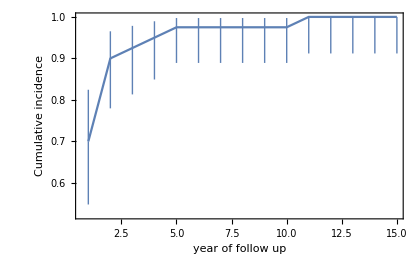

```mathematica
ListPlot[datatemp10,
Joined->True,
BaseStyle->{FontSize->16},Axes->False,
Frame->{True,True,False,False},FrameStyle->Thickness[0.005],FrameTicksStyle->Thickness[0.005],PlotRange->All,AspectRatio->1/GoldenRatio,ImageSize->{420,280},
IntervalMarkersStyle->Automatic,
Frame->True,
FrameLabel->{"year of follow up","Cumulative incidence"},
PlotRange->{{0,15.3},All}
]
```

```mathematica
(* Fitting the data on TST- to TST+ conversion: using likelihood function *)

n=1;

datasetT=datatemp1[[n]]

Clear[TST];
fmin=10^-10;
TST[t_,{c1_,c2_,f_}]:=Module[{x=1-f*Exp[-c1*t]-(1-f)*Exp[-c2*t]},If[x>1-fmin,1-fmin,x]];
func[t_,pars_]:=TST[t,pars];

logL[tdata_,pars_]:=-Total[Map[#[[2]]*#[[3]]*Log[TST[#[[1]],pars]]+(#[[3]]-#[[2]]*#[[3]])*Log[(1-TST[#[[1]],pars])]&,tdata]];
```

{{1,0.7,40},{2,0.9,40},{3,0.925,40},{4,0.95,40},{5,0.975,40},{6,0.975,40},{7,0.975,40},{8,0.975,40},{9,0.975,40},{10,0.975,40},{11,1.,40},{12,1.,40},{13,1.,40},{14,1.,40},{15,1.,40}}

```mathematica
(* two exponents: defining initial guesses for the model *)
AllPars0={
{1.5692878555735092,0.2692073988662197,0.8599884104661814}
};
FitPars={1,1,1};

Par0=AllPars0[[n]];
eps=10;

AllPars={c1,c2,f};
Npar=Length[AllPars];
ParF=Table[If[FitPars[[i]]==1,AllPars[[i]],Par0[[i]]],{i,1,Npar}];
ConPars=Table[0,{Npar}];
ConPars=ReplacePart[ConPars,1,{{1},{2}}];

Print["Parameters to be fitted are ",Cases[AllPars*FitPars,x_?(!NumericQ[#]&)]];
Print["Parameters to be constrained (i.e. to be > 0) are ",Cases[AllPars*ConPars,x_?(!NumericQ[#]&)]];

logL[datasetT,Par0]
```

Parameters to be fitted are {c1,c2,f}

Parameters to be constrained (i.e. to be > 0) are {c1,c2}

85.8433

```mathematica
tStart=SessionTime[];
sol=minimum2r[datasetT,logL,ParF,Par0,ConPars]
tEnd=SessionTime[];
Print["Simulations ran for ",tEnd-tStart," sec"];
If[NumericQ[sol[[1]]],Par0=ParF/.sol[[2]]];
Par0
```

{85.8433,{c1→1.56928,c2→0.269207,f→0.859989}}

Simulations ran for 0.00534 sec

{1.56928,0.269207,0.859989}

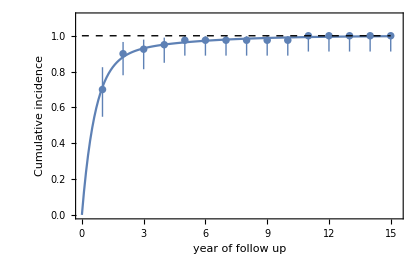

```mathematica
{t1,t2,f0}={Log[2]/Par0[[1]],Log[2]/Par0[[2]],Par0[[3]]};
ttemp1=Table[{t,func[t,Par0]},{t,0,15,0.1}];

datatemp10=AddErrorBar[datasetT];
Show[
ListPlot[{datatemp10},
Epilog->{
{Dashed,Line[{{0,1},{15,1}}]}
},
FrameTicks->Automatic,
FrameLabel->{"year of follow up","Cumulative incidence"},
PlotRange->{{0,15.3},{0,1.1052}},
BaseStyle->{FontSize->16},Axes->False,
Frame->{True,True,False,False},FrameStyle->Thickness[0.005],FrameTicksStyle->Thickness[0.005],PlotRange->All,AspectRatio->1/GoldenRatio,ImageSize->{420,280},
IntervalMarkersStyle->Automatic,
Frame->True,
FrameLabel->{"year of follow up","Cumulative incidence"}
],
ListPlot[{ttemp1},
Joined->True,
PlotMarkers->None
]
]
```

### TST- to TB+: homogeneous vs. heterogeneous Poisson model with a delay

```mathematica
data1=Import["badger_art49-all-edited.csv","CSV"];
Transpose[{Range[Length[data1[[1]]]],data1[[1]]}]//TableForm
```

1 | Initial status
2 | Total number of nurses
3 | Conversion
4 | year
5 | Number of cases
6 | Total number of cases
7 | Paper

```mathematica
Split[Drop[data1[[All,1]],1]][[All,1]];
status={"TST-","TST+"};

Split[Drop[data1[[All,3]],1]][[All,1]];
conversion={
{"TST- to TST+","TST+ to TB","TST- to TB"},
{"TST+ to TB"}
};

numbers=Table[
Cases[data1,x_?(#[[1]]==status[[i]]&&#[[3]]!=conversion[[1,3]]&):>{x[[2]],x[[6]]}],{i,1,Length[status]}
][[All,1]]
```

{{362,40},{374,31}}

```mathematica
alldata=
Table[
Table[
Cases[data1,x_?(#[[1]]==status[[i]]&&#[[3]]==conversion[[i,j]]&):>{x[[4]],N[100*x[[5]]/x[[6]]],x[[6]],x[[2]]}],{j,1,Length[conversion[[i]]]}
],{i,1,Length[status]}]
```

{{{{1,70.,40,362},{2,20.,40,362},{3,2.5,40,362},{4,2.5,40,362},{5,2.5,40,362},{6,0.,40,362},{7,0.,40,362},{8,0.,40,362},{9,0.,40,362},{10,0.,40,362},{11,2.5,40,362},{12,0.,40,362},{13,0.,40,362},{14,0.,40,362},{15,0.,40,362}},{{1,65.,40,362},{2,17.5,40,362},{3,2.5,40,362},{4,2.5,40,362},{5,2.5,40,362},{6,5.,40,362},{7,2.5,40,362},{8,0.,40,362},{9,0.,40,362},{10,0.,40,362},{11,2.5,40,362},{12,0.,40,362},{13,0.,40,362},{14,0.,40,362},{15,0.,40,362}},{{1,17.5,40,362},{2,37.5,40,362},{3,22.5,40,362},{4,12.5,40,362},{5,0.,40,362},{6,2.5,40,362},{7,5.,40,362},{8,0.,40,362},{9,0.,40,362},{10,0.,40,362},{11,0.,40,362},{12,0.,40,362},{13,0.,40,362},{14,2.5,40,362},{15,0.,40,362}}},{{{1,16.129,31,374},{2,16.129,31,374},{3,29.0323,31,374},{4,6.45161,31,374},{5,3.22581,31,374},{6,9.67742,31,374},{7,6.45161,31,374},{8,6.45161,31,374},{9,6.45161,31,374},{10,0.,31,374},{11,0.,31,374},{12,0.,31,374},{13,0.,31,374},{14,0.,31,374},{15,0.,31,374}}}}

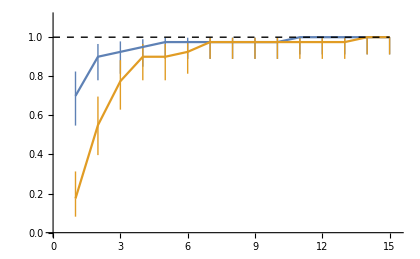

```mathematica
(* TST- to TB and TST+ to TB *)

datatemp={alldata[[1,1]],alldata[[1,3]]};
tempdata0=Map[Transpose[{#[[All,1]],(Accumulate/@Transpose[#])[[2]]}]&,datatemp];

labs4={"TST- to TST+ (n="<>ToString[numbers[[1,2]]]<>")","TST- to TB (n="<>ToString[numbers[[1,2]]]<>")"};

datatemp1=Map[Transpose[{#[[All,1]],(Accumulate/@Transpose[#])[[2]]/100,#[[All,3]]}]&,datatemp];
datatemp10=Map[AddErrorBar[#]&,datatemp1];
ListPlot[datatemp10,
Joined->True,
Epilog->{
{Dashed,Line[{{0,1},{15,1}}]}
},
FrameLabel->{"year of follow up","Cumulative incidence"},
PlotRange->{{0,15.3},{0,1.102}}
]
```

```mathematica
(* Fitting the data on TST- to TB: using likelihood function *)

temp1=Map[{#[[1]],#[[2]]/100,#[[3]]}&,alldata[[1,3]]];
datasetT=Map[Transpose[{#[[All,1]],(Accumulate/@Transpose[#])[[2]],#[[All,3]]}]&,{temp1}][[1]]

Clear[TB];
fmin=10^-10;
TB[t_,{c1_,c2_,f_,delay_}]:=If[t<delay,0,Module[{x=1-f*Exp[-c1*(t-delay)]-(1-f)*Exp[-c2*(t-delay)]},If[x>1-fmin,1-fmin,x]]];
func[t_,pars_]:=TB[t,pars];

logL[tdata_,pars_]:=-Total[Map[#[[2]]*#[[3]]*Log[TB[#[[1]],pars]]+(#[[3]]-#[[2]]*#[[3]])*Log[(1-TB[#[[1]],pars])]&,tdata]];
```

{{1,0.175,40},{2,0.55,40},{3,0.775,40},{4,0.9,40},{5,0.9,40},{6,0.925,40},{7,0.975,40},{8,0.975,40},{9,0.975,40},{10,0.975,40},{11,0.975,40},{12,0.975,40},{13,0.975,40},{14,1.,40},{15,1.,40}}

```mathematica
Par0={0.9439416923598668,0.2671206747144021,0.75,0.7559270039123561};
FitPars={1,1,0,1};

Par0={0.6105177691987527,0,1,0.6783012469789956};
FitPars={1,0,0,1};

Par0={0.6105177691987527,0,1,0};
FitPars={1,0,0,0};

Par0={0.6105177691987527,0,0.9,0};
FitPars={1,0,1,0};

(* Best fit *)
Par0={0.768367414662222,0.174659918124891,0.893611198494644,0.7328499246464047};
FitPars={1,1,1,1};

eps=10;

AllPars={c1,c2,f,tau};
Npar=Length[AllPars];
ParF=Table[If[FitPars[[i]]==1,AllPars[[i]],Par0[[i]]],{i,1,Npar}];
ConPars=Table[1,{Npar}];
ConPars=ReplacePart[ConPars,1,{{1},{2}}];

Print["Parameters to be fitted are ",Cases[AllPars*FitPars,x_?(!NumericQ[#]&)]];
Print["Parameters to be constrained (i.e. to be > 0) are ",Cases[AllPars*ConPars,x_?(!NumericQ[#]&)]];

logL[datasetT,Par0]
```

Parameters to be fitted are {c1,c2,f,tau}

Parameters to be constrained (i.e. to be > 0) are {c1,c2,f,tau}

138.593

```mathematica
tStart=SessionTime[];
sol=minimum2r[datasetT,logL,ParF,Par0,ConPars]
tEnd=SessionTime[];
Print["Simulations ran for ",tEnd-tStart," sec"];
If[NumericQ[sol[[1]]],Par0=ParF/.sol[[2]]];
Par0
```

{138.593,{c1→0.768364,c2→0.174661,f→0.893611,tau→0.732854}}

Simulations ran for 0.00473 sec

{0.768364,0.174661,0.893611,0.732854}

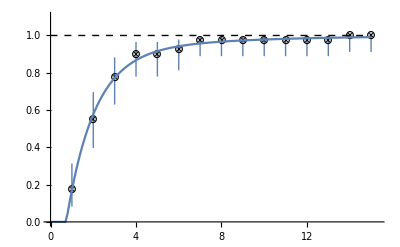

```mathematica
Clear[t1,t2,f0,tau0];
{t1,t2,f0,tau0}={Log[2]/c1,Log[2]/c2,f,tau}/.sol[[2]];
ttemp1=Table[{t,func[t,ParF/.sol[[2]]]},{t,0,15,0.1}];

datatemp10=AddErrorBar[datasetT];
myFig1=Show[
ListPlot[{datatemp10},
Joined->False,
Epilog->{
{Dashed,Line[{{0,1},{15,1}}]}
},
FrameTicks->Automatic,
FrameLabel->{"year of follow up","Cumulative incidence"},
PlotRange->{{0,15.3},{0,1.102}}
]/.Point[pts_List]:>(Text[Style["⊗",12,Bold,Black],#]&/@pts),
ListPlot[{ttemp1},
Joined->True,
PlotMarkers->None
]
]
```

### TST+ to TB+: homogeneous vs. heterogeneous Poisson model with a delay

```mathematica
data1=Import["badger_art49-all-edited.csv","CSV"];
Transpose[{Range[Length[data1[[1]]]],data1[[1]]}]//TableForm
```

1 | Initial status
2 | Total number of nurses
3 | Conversion
4 | year
5 | Number of cases
6 | Total number of cases
7 | Paper

```mathematica
Split[Drop[data1[[All,1]],1]][[All,1]];
status={"TST-","TST+"};

Split[Drop[data1[[All,3]],1]][[All,1]];
conversion={
{"TST- to TST+","TST+ to TB","TST- to TB"},
{"TST+ to TB"}
};

numbers=Table[
Cases[data1,x_?(#[[1]]==status[[i]]&&#[[3]]!=conversion[[1,3]]&):>{x[[2]],x[[6]]}],{i,1,Length[status]}
][[All,1]]
```

{{362,40},{374,31}}

```mathematica
alldata=
Table[
Table[
Cases[data1,x_?(#[[1]]==status[[i]]&&#[[3]]==conversion[[i,j]]&):>{x[[4]],N[100*x[[5]]/x[[6]]],x[[6]],x[[2]]}],{j,1,Length[conversion[[i]]]}
],{i,1,Length[status]}]
```

{{{{1,70.,40,362},{2,20.,40,362},{3,2.5,40,362},{4,2.5,40,362},{5,2.5,40,362},{6,0.,40,362},{7,0.,40,362},{8,0.,40,362},{9,0.,40,362},{10,0.,40,362},{11,2.5,40,362},{12,0.,40,362},{13,0.,40,362},{14,0.,40,362},{15,0.,40,362}},{{1,65.,40,362},{2,17.5,40,362},{3,2.5,40,362},{4,2.5,40,362},{5,2.5,40,362},{6,5.,40,362},{7,2.5,40,362},{8,0.,40,362},{9,0.,40,362},{10,0.,40,362},{11,2.5,40,362},{12,0.,40,362},{13,0.,40,362},{14,0.,40,362},{15,0.,40,362}},{{1,17.5,40,362},{2,37.5,40,362},{3,22.5,40,362},{4,12.5,40,362},{5,0.,40,362},{6,2.5,40,362},{7,5.,40,362},{8,0.,40,362},{9,0.,40,362},{10,0.,40,362},{11,0.,40,362},{12,0.,40,362},{13,0.,40,362},{14,2.5,40,362},{15,0.,40,362}}},{{{1,16.129,31,374},{2,16.129,31,374},{3,29.0323,31,374},{4,6.45161,31,374},{5,3.22581,31,374},{6,9.67742,31,374},{7,6.45161,31,374},{8,6.45161,31,374},{9,6.45161,31,374},{10,0.,31,374},{11,0.,31,374},{12,0.,31,374},{13,0.,31,374},{14,0.,31,374},{15,0.,31,374}}}}

{{{1,17.5},{2,55.},{3,77.5},{4,90.},{5,90.},{6,92.5},{7,97.5},{8,97.5},{9,97.5},{10,97.5},{11,97.5},{12,97.5},{13,97.5},{14,100.},{15,100.}},{{1,16.129},{2,32.2581},{3,61.2903},{4,67.7419},{5,70.9677},{6,80.6452},{7,87.0968},{8,93.5484},{9,100.},{10,100.},{11,100.},{12,100.},{13,100.},{14,100.},{15,100.}}}

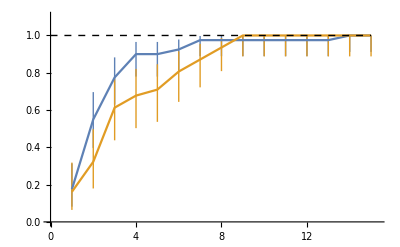

```mathematica
(* TST- to TB and TST+ to TB *)

datatemp={alldata[[1,3]],alldata[[2,1]]};
tempdata0=Map[Transpose[{#[[All,1]],(Accumulate/@Transpose[#])[[2]]}]&,datatemp]

labs4={"TST- to TB (n="<>ToString[numbers[[1,2]]]<>")","TST+ to TB (n="<>ToString[numbers[[2,2]]]<>")"};

datatemp1=Map[Transpose[{#[[All,1]],(Accumulate/@Transpose[#])[[2]]/100,#[[All,3]]}]&,datatemp];
datatemp10=Map[AddErrorBar[#]&,datatemp1];
ListPlot[datatemp10,
Joined->True,
Epilog->{
{Dashed,Line[{{0,1},{15,1}}]}
},
FrameLabel->{"year of follow up","Cumulative incidence"},
PlotRange->{{0,15.3},{0,1.102}}
]
```

```mathematica
(* Fitting the data on TST+ to TB: using likelihood function *)

temp1=Map[{#[[1]],#[[2]]/100,#[[3]]}&,alldata[[2,1]]];
datasetT=Map[Transpose[{#[[All,1]],(Accumulate/@Transpose[#])[[2]],#[[All,3]]}]&,{temp1}][[1]]

Clear[TB];
fmin=10^-10;
TB[t_,{c1_,c2_,f_,delay_}]:=If[t<delay,0,Module[{x=1-f*Exp[-c1*(t-delay)]-(1-f)*Exp[-c2*(t-delay)]},If[x>1-fmin,1-fmin,x]]];
func[t_,pars_]:=TB[t,pars];

logL[tdata_,pars_]:=-Total[Map[#[[2]]*#[[3]]*Log[TB[#[[1]],pars]]+(#[[3]]-#[[2]]*#[[3]])*Log[(1-TB[#[[1]],pars])]&,tdata]];
```

{{1,0.16129,31},{2,0.322581,31},{3,0.612903,31},{4,0.677419,31},{5,0.709677,31},{6,0.806452,31},{7,0.870968,31},{8,0.935484,31},{9,1.,31},{10,1.,31},{11,1.,31},{12,1.,31},{13,1.,31},{14,1.,31},{15,1.,31}}

```mathematica
Par0={0.31661708687261503,0,1,0};
FitPars={1,0,0,0};

Par0={0.3769399141972494,0.373417909495974,5.41221000715849*^-7,0.6407777882727211};
FitPars={1,1,1,1};

Par0={0.31661708687261503,0.002,0.999,0};
FitPars={1,1,1,0};

(* Best fit *)
Par0={0.3734183731321119,0,1,0.6407861004014537};
FitPars={1,0,0,1};

eps=10;

AllPars={c1,c2,f,tau};
Npar=Length[AllPars];
ParF=Table[If[FitPars[[i]]==1,AllPars[[i]],Par0[[i]]],{i,1,Npar}];
ConPars=Table[1,{Npar}];
ConPars=ReplacePart[ConPars,1,{{1},{2}}];

Print["Parameters to be fitted are ",Cases[AllPars*FitPars,x_?(!NumericQ[#]&)]];
Print["Parameters to be constrained (i.e. to be > 0) are ",Cases[AllPars*ConPars,x_?(!NumericQ[#]&)]];

logL[datasetT,Par0]
```

Parameters to be fitted are {c1,tau}

Parameters to be constrained (i.e. to be > 0) are {c1,c2,f,tau}

132.841

```mathematica
tStart=SessionTime[];
sol=minimum2r[datasetT,logL,ParF,Par0,ConPars]
tEnd=SessionTime[];
Print["Simulations ran for ",tEnd-tStart," sec"];
If[NumericQ[sol[[1]]],Par0=ParF/.sol[[2]]];
Par0
```

{132.841,{c1→0.373418,tau→0.640785}}

Simulations ran for 0.00397 sec

{0.373418,0,1,0.640785}

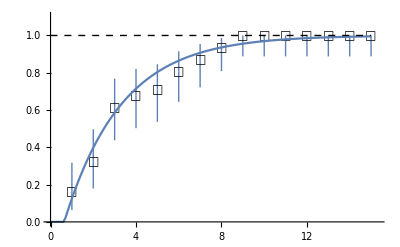

```mathematica
Clear[t1,t2,f0,tau0];
{t1,tau0}={Log[2]/c1,tau}/.sol[[2]];
ttemp1=Table[{t,func[t,ParF/.sol[[2]]]},{t,0,15,0.1}];

datatemp10=AddErrorBar[datasetT];
myFig2=Show[
ListPlot[{datatemp10},
Joined->False,
Epilog->{
{Dashed,Line[{{0,1},{15,1}}]}
},
FrameTicks->Automatic,
FrameLabel->{"year of follow up","Cumulative incidence"},
PlotRange->{{0,15.3},{0,1.102}}
]/.Point[pts_List]:>(Text[Style["□",12,Bold,Black],#]&/@pts),
ListPlot[{ttemp1},
Joined->True,
PlotMarkers->None
]
]
```